On impact - wrench/ pile - driver  locomotion for a micro - robot
Lessons:  need a flat impact region -- any curve will dampen response (slight tilt will cause robots to roll around end).  Want the tip very sharp.  Keeping roobt level is hard -- even a slight tilt causes problems.
http://www.fooduniversity.com/foodu/food_c/basic_knife_skills/Knives/basic_knife_bevel_angle.htm
recommends 12 degree point angle.

```mathematica
Resources:
[1] coefficient of restitution: Frontal Impact of Rolling spheres, http://itzhak.green.gatech.edu/rotordynamics/Predicting%20the%20coefficient%20of%20restitution%20of%20impacting%20spheres.pdf
aluminum-aluminum 0.69
brass-brass 0.72
steel-stell 095
brass-steel 0.72
brass-aluminum 0.61
steel-aluminum 0.55
```

### We can apply a force of Fm = to a bead of radius r If this force is applied along a distance L, how fast is the ball moving? What is the momentum? Average impact force x distance traveled = change in kinetic energy

### Physics of Hammering: energy is proportional to the length of L and the cube of the ball radius.

```mathematica
ImpactAccel[r]
```

3.98471

```mathematica
Solve[L==1/2 ImpactAccel[r] t^2,t]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{t→-0.708462 √L},{t→0.708462 √L}}

```mathematica
t->0.708461825766057 √L
```

t→0.708462 √L

```mathematica
ImpactVel = ImpactAccel[r]*0.708461825766057 √L
```

2.82302 √L

```mathematica
ImpactEnergy[rad_,L_]:=1/2  massCapsule[rad]* (ImpactAccel[r]*0.708461825766057 √L)^2
ImpactEnergy[rad,L]
```

131025. L rad^3

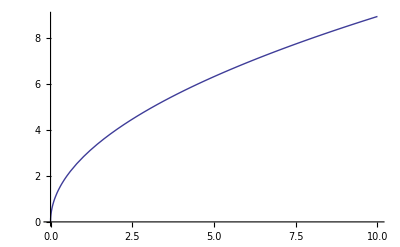

```mathematica
Plot[2.823017313370989 √L,{L,0,10},PlotLabel->]
```

## Gauss Gun http://m.metamorphosite.com/increase-gauss-rifle-speed http://www.physicsforums.com/showthread.php?t=275045 http://isites.harvard.edu/fs/docs/icb.topic1216311.files/Project%20resources/Gauss%20Gun/Gauss%20Rifle.pdf

```mathematica
The Potential Energy between two dipoles of radius r separated by distance d
```

```mathematica
Msat = 1.36 10^6;
(*A/m, from An MRI-powered and controlled actuator technology for tetherless robotic interventions *)
DensityFerrous = 7850;(*kg/m^3*)
μ0 = 4π 10^-7;
magMoment[rad_] := 4/3 π rad^3 Msat (*A m^2*)
ForceMag[rad_,grad_]:=magMoment[rad] grad
ForceAlignDipoles[d_,rad_]:=- (3μ0  magMoment[rad] magMoment[rad])/(2 π d^4) (* from wikipedia == -(1.947180832027187*^7 rad^6)/d^4*)
massCapsule[rad_]:=4/3 π rad^3 DensityFerrous;
AccelCap[d_,rad_]:=ForceAlignDipoles[d,rad]/massCapsule[rad]

ImpactAccel[rad_]:=  ForceMag[rad,0.023]/massCapsule[rad]
```

```mathematica
AccelCap[dist,radius]
```

-(592.172 radius^3)/dist^4

{{p→InterpolatingFunction[{{0.,0.205}},<>]}}

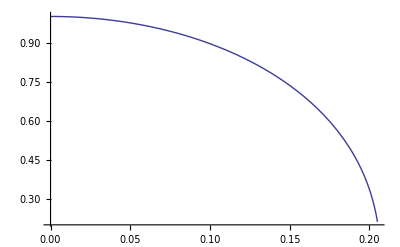

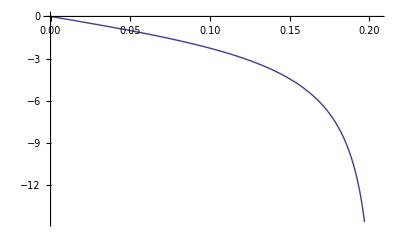

```mathematica
tf = 20.5/100;
s=NDSolve[{p''[t]==ForceAlignDipoles[p[t],1/10],p[0]==1,p'[0]==0},p ,{t,0,tf}]
Plot[Evaluate[p[t]/.s],{t,0,tf}]
Plot[Evaluate[p'[t]/.s],{t,0,tf}]
```

```mathematica
∫_0^T AccelCap[r,d[t]]ⅆt
```

∫_0^T -(592.172 r^3)/d[t]^4ⅆt

```mathematica
∫_0^T ∫_0^T AccelCap[r,d[t]]ⅆtⅆt
```

```mathematica
Solve[d[T]==-592.1722060718147 r^3 ∫_0^T ∫_0^T 1/d[t]^4 ⅆtⅆt&&d[0]==1,d[t],t]
```

Solve::bdomv: Warning: t is not a valid domain specification. Mathematica is assuming it is a variable to eliminate.

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[d[T]==-592.172 r^3 ∫_0^T ∫_0^T 1/d[t]^4 ⅆtⅆt&&d[0]==1,d[t],t]

## Using Events to Optimize

```mathematica
Some basic design constraints:
```

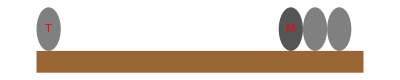

```mathematica
DrawGaussGun[myL_, mRad_]:=Module[{tx,ty,mx,my},
Graphics[{
Brown,Rectangle[{-mRad,-mRad},{myL+6mRad,0}],
(*trigger*)
tx = 0;
ty = mRad;
Gray,Disk[{tx,ty},mRad],
Red,Text["T",{tx,ty}],
mx = myL;
Darker[Gray],Disk[{mx,ty},mRad],
Red,Text["M",{mx,ty}],

Gray,Disk[{mx+2mRad,ty},mRad],
Gray,Disk[{mx+4mRad,ty},mRad],

}]];
DrawGaussGun[myL, mRad]
```

```mathematica
(*tutorial/NDSolveEventLocator*)
Needs["DifferentialEquations`NDSolveProblems`"];
Needs["DifferentialEquations`NDSolveUtilities`"];
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];
```

-7.02129

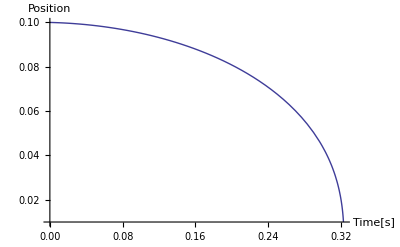

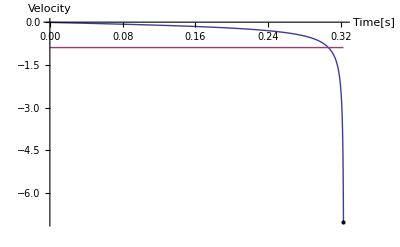

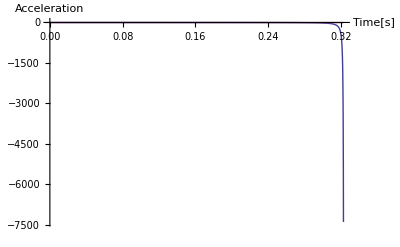

```mathematica
tf = 1000;
myL =1/10;
mRad = 0.005; (*ball radius, m*)
s=NDSolve[{p''[t]==ForceAlignDipoles[p[t],mRad]/massCapsule[mRad],p[0]==myL,p'[0]==-.01},p ,{t,0,tf}, Method->{"EventLocator", "Event"->p[t]-2mRad}];
end = InterpolatingFunctionDomain[First[p /. s]][[1,-1]];
Evaluate[p'[end]/.s]⟦1⟧
Plot[Evaluate[p[t]/.s],{t,0,end},AxesLabel-> {"Time[s]","Position"}]
Plot[{Evaluate[p'[t]/.s],-2.823017313370989 √myL},{t,0,end},AxesLabel-> {"Time[s]","Velocity"},PlotRange->All,Epilog->{Point[{end,Evaluate[p'[end]/.s]⟦1⟧}]}]
Plot[{Evaluate[p''[t]/.s],-ImpactAccel[mRad]},{t,0,end},AxesLabel-> {"Time[s]","Acceleration"},PlotRange->All]
```

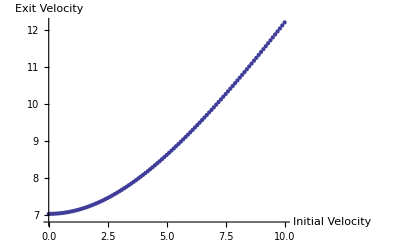

```mathematica
pts = Table[
initVel = i/10;
s=NDSolve[{p''[t]==ForceAlignDipoles[p[t],mRad]/massCapsule[mRad],p[0]==myL,p'[0]==-initVel},p ,{t,0,∞}, Method->{"EventLocator", "Event"->p[t]-2mRad}];
end = InterpolatingFunctionDomain[First[p /. s]][[1,-1]];
fvel = Evaluate[p'[end]/.s]⟦1⟧;
{initVel,-fvel},{i,0,100}];
ListPlot[pts,AxesLabel-> {"Initial Velocity","Exit Velocity"}]
```

Compute the change in energy as a function of initial velocity (almost zero effect)

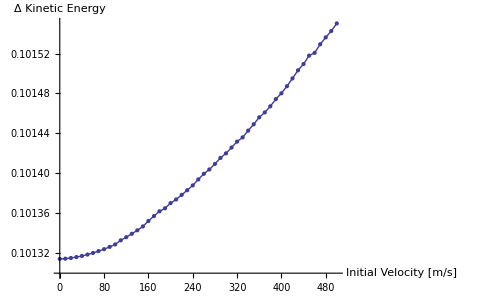

```mathematica
pts = Table[
initVel = i/10;
s=NDSolve[{p''[t]==ForceAlignDipoles[p[t],mRad]/massCapsule[mRad],p[0]==myL,p'[0]==-initVel},p ,{t,0,∞}, Method->{"EventLocator", "Event"->p[t]-2mRad}];
end = InterpolatingFunctionDomain[First[p /. s]][[1,-1]];
fvel = Evaluate[p'[end]/.s]⟦1⟧;
{initVel,(1/2 fvel^2-1/2 initVel^2)massCapsule[mRad]},{i,0,5000,100}];
ListPlot[pts,Joined->True,Mesh->All,AxesLabel-> {"Initial Velocity [m/s]","Δ Kinetic Energy"}]
```

Compute the change in energy as a function of initial separation  (big effect)
starting 1 diameter away gives you 87.5%, 2 diameters 96.3%, 3 diameters 98.4%, 4 diameters 0.992%
TODO:  draw the balls on the bottom

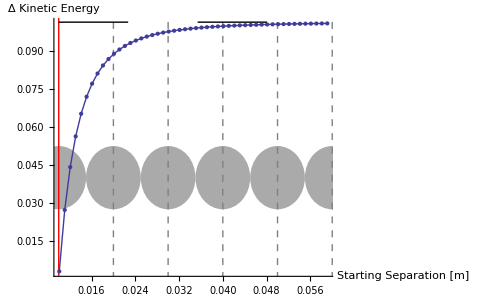

```mathematica
pts = Table[
initVel = 1;
varyL = 2mRad + i/10000;
s=NDSolve[{p''[t]==ForceAlignDipoles[p[t],mRad]/massCapsule[mRad],p[0]==varyL,p'[0]==-initVel},p ,{t,0,∞}, Method->{"EventLocator", "Event"->p[t]-2mRad}];
end = InterpolatingFunctionDomain[First[p /. s]][[1,-1]];
fvel = Evaluate[p'[end]/.s]⟦1⟧;
{varyL,(1/2 fvel^2-1/2 initVel^2)massCapsule[mRad]},{i,1,500,10}];
maxEnergyLongL =(
s=NDSolve[{p''[t]==ForceAlignDipoles[p[t],mRad]/massCapsule[mRad],p[0]==1000,p'[0]==-initVel},p ,{t,0,∞}, Method->{"EventLocator", "Event"->p[t]-2mRad}];
end = InterpolatingFunctionDomain[First[p /. s]][[1,-1]];
fvel = Evaluate[p'[end]/.s]⟦1⟧;
(1/2 fvel^2-1/2 initVel^2)massCapsule[mRad]
);

ListPlot[pts,AxesLabel-> {"Starting Separation [m]","Δ Kinetic Energy"},Joined->True,Mesh->All,Prolog->{
Red,Disk[{0,0.04},{mRad,2.5mRad}],
Green,Disk[{0,0.04},{mRad,2.5mRad},{-π/2,π/2}],
Lighter[Gray],Table[Disk[{2 k mRad,0.04},{mRad,2.5mRad}],{k,1,6}],
Red,Line[{{ 2mRad,0},{ 2mRad,1}}],
Gray,Dashed, Table[Line[{{ (2+k)mRad,0},{ (2+k)mRad,1}}],{k,2,10,2}],
(*limit point*)
Black,Dashing[1], Line[{{2 mRad,maxEnergyLongL},{50,maxEnergyLongL}}]
},
PlotRange->All,AxesOrigin->{-mRad,0}]
```

```mathematica
Table[
initVel = 1;
varyL = 2i mRad ;
s=NDSolve[{p''[t]==ForceAlignDipoles[p[t],mRad]/massCapsule[mRad],p[0]==varyL,p'[0]==-initVel},p ,{t,0,∞}, Method->{"EventLocator", "Event"->p[t]-2mRad}];
end = InterpolatingFunctionDomain[First[p /. s]][[1,-1]];
fvel = Evaluate[p'[end]/.s]⟦1⟧;
{varyL,(1/2 fvel^2-1/2 initVel^2)massCapsule[mRad]/maxEnergyLongL},{i,2,5}]
```

{{0.02,0.875},{0.03,0.962963},{0.04,0.984375},{0.05,0.992}}

Optimal Intermagnet spacing?  This is a 2D plot, with left spread (left magnet to steel) on x axis and (steel to right magnet) on y-axis.
The steel must start closer to the left magnet than the right magnet

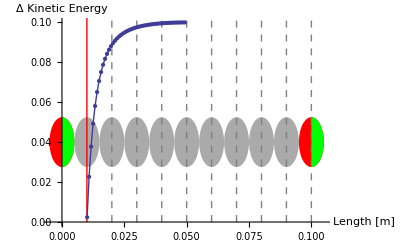

```mathematica
pts = Table[
initVel =0;
varyL =20mRad;(*distance between magnets*)
initPos =2mRad + (varyL-4 mRad)/2 i/500;
s=NDSolve[{p''[t]==(ForceAlignDipoles[p[t],mRad] - ForceAlignDipoles[varyL-p[t],mRad])/massCapsule[mRad],p[0]==initPos,p'[0]==-initVel},p ,{t,0,∞}, Method->{"EventLocator", "Event"->p[t]-2mRad}];
end = InterpolatingFunctionDomain[First[p /. s]][[1,-1]];
fvel = Evaluate[p'[end]/.s]⟦1⟧;
{initPos,(1/2 fvel^2-1/2 initVel^2)massCapsule[mRad]},{i,1,500,10}];


ListPlot[pts,AxesLabel-> {"Length [m]","Δ Kinetic Energy"},Joined->True,Mesh->All,Prolog->{
Red,Disk[{0,0.04},{mRad,2.5mRad}],
Green,Disk[{0,0.04},{mRad,2.5mRad},{-π/2,π/2}],
Lighter[Gray],Table[Disk[{2 k mRad,0.04},{mRad,2.5mRad}],{k,1,varyL/(2mRad)-1}],

Red,Disk[{varyL,0.04},{mRad,2.5mRad}],
Green,Disk[{varyL,0.04},{mRad,2.5mRad},{-π/2,π/2}],

Red,Line[{{ 2mRad,0},{ 2mRad,1}}],
Gray,Dashed, Table[Line[{{ (2+k)mRad,0},{ (2+k)mRad,1}}],{k,2,varyL/(mRad),2}]
},
PlotRange->{{-mRad, varyL+mRad},Automatic},AxesOrigin->{0,0}]
```

```mathematica
pts
```

{{0.04,1.58462×10^6},{0.04,1190.64},{0.04,171.203},{0.04,53.2871},{0.04,23.0877},{0.04,12.0416},{0.04,7.07703},{0.04,4.5231},{0.04,3.07736},{0.04,2.19836},{0.04,1.6335},{0.04,1.25406},{0.04,0.989803},{0.04,0.800118},{0.04,0.660445},{0.04,0.555321},{0.04,0.474682},{0.04,0.411789},{0.04,0.362008},{0.04,0.322085},{0.04,0.289689},{0.04,0.263119},{0.04,0.241115},{0.04,0.22273},{0.04,0.207243},{0.04,0.194097},{0.04,0.182859},{0.04,0.173188},{0.04,0.164814},{0.04,0.157519},{0.04,0.151126},{0.04,0.145495},{0.04,0.140506},{0.04,0.136063},{0.04,0.132086},{0.04,0.128507},{0.04,0.125269},{0.04,0.122324},{0.04,0.11963},{0.04,0.117153},{0.04,0.114861},{0.04,0.112729},{0.04,0.110732},{0.04,0.10885},{0.04,0.107064},{0.04,0.105357},{0.04,0.103714},{0.04,0.102121},{0.04,0.100564},{0.04,0.0990302}}